{{L:,40.2},{m:,100},{N:,22},{kappa:,0.1},{sigma:,0.000666},{kappa_sigma_r:,150.15},{Delta:,0.2},{Extension Minimum:,0},{Extension Maximum:,60},{e0:,0.0222},{Beta:,38.6817},{etab_b:,3.2}}

Backbone spring constant κ:

0.1

Base-pair spring constant σ:

0.000666

Base-pair energy ϵ:

0.0222

κ/σ ratio:

150.15

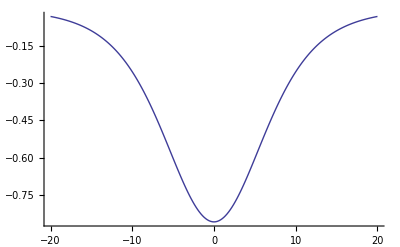

```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
Parameters=Import["Parameters"]
Potential=Import["Potential_Data.out","Table"];

<<Units`
<<PhysicalConstants`

fsTitle=24;
fsAxesLabel=18;
fs2=16;

T=300 SI[Kelvin];
n=Parameters[[3,2]];
Print["Backbone spring constant κ:"]
κ=Parameters[[4,2]]
Print["Base-pair spring constant σ:"]
σ=Parameters[[5,2]]
Print["Base-pair energy ϵ:"]
ϵ=Parameters[[10,2]](*eV*)
Print["κ/σ ratio:"]
κσr=Parameters[[6,2]]
Δ=Parameters[[7,2]];

umin=Parameters[[8,2]];
umax=Parameters[[9,2]];


β=Parameters[[11,2]];(*eV^-1*)

ToNewton=Convert[ElectronVolt/Angstrom,Newton] SI[Pico Newton]^-1;(*Converts eV/Å to pN*)
ToForceDimension[f_]:=(f (κ/(4 β))^(1/2)) ToNewton;
ToDimension[η_]:=η (((κ β)/4)^(-(1/2)))(*Converts to Å*)

ListLinePlot[Potential,PlotStyle->{Thick},AxesOrigin->{0,0},PlotRange->All]

IntactPF=Import["Intact/PartitionFunction_0_0.out","Table"];
IntactFE=Import["Intact/FreeEnergy_0_0.out","Table"];
IntactdFE=Import["Intact/dFreeEnergy_0_0.out","Table"];

FrayedData=Table[{
Import["Frayed/PartitionFunction_0_"<>ToString[i]<>".out","Table"],
Import["Frayed/FreeEnergy_0_"<>ToString[i]<>".out","Table"],
Import["Frayed/dFreeEnergy_0_"<>ToString[i]<>".out","Table"]
}
,{i,1,(n-1)}
];
```

## Analysis

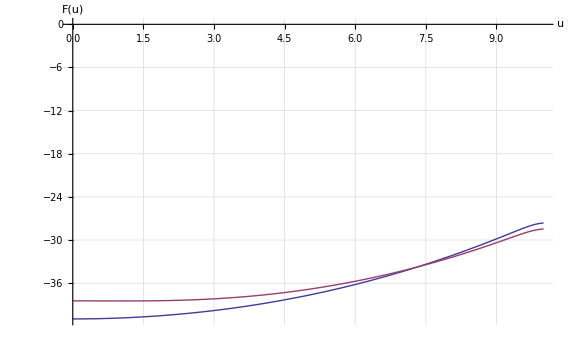

Dimensional Force = 70.1536 pN
Dimensional Extension = 7.31078 Å

```mathematica
fs=1;
IntactFEcurve=Interpolation[IntactFE ];
IntersectingFEcurve=Interpolation[FrayedData[[fs,2]]];

Plot[{IntactFEcurve[x],IntersectingFEcurve[x]},{x,0,10},
PlotStyle->Thick,
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},
LabelStyle->{"Times",FontSize->fs2}
]

u=x/.FindRoot[IntactFEcurve[x]-IntersectingFEcurve[x],{x,5}];
IntersectingdFEcurve=Interpolation[FrayedData[[1,3]]];
Ext=ToDimension[u];
Force=ToForceDimension[IntersectingdFEcurve[u]];

Print["\nDimensional Force = ",Force pN,"\nDimensional Extension = ",u Å,"\n"]
Export["N"<>ToString[n]<>"_sim.data",{{n,Force,κσr}},"Table"];
```